```mathematica
L=1;
Lx=1;
Ly=1;
```

```mathematica
g=1;
```

```mathematica
f0=1;
```

```mathematica
f[x_,y_]=Exp[((x/L-1/2)^2+(y/L-1/2)^2)/1000] 
f[x_,y_]=Cos[2*Pi*((x/Lx+y/Ly))]
gf[x_,y_]=Grad[f[x,y],{x,y, z}]
```

ⅇ^(((-1/2+x)^2+(-1/2+y)^2)/1000)

Cos[2 π (x+y)]

{-2 π Sin[2 π (x+y)],-2 π Sin[2 π (x+y)],0}

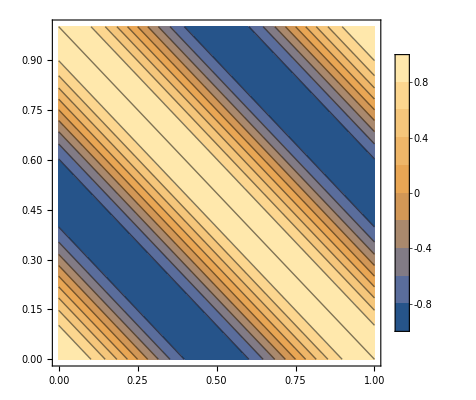

```mathematica
ContourPlot[f[x,y],{x,0,1},{y,0, 1}, PlotLegends->Automatic]
```

```mathematica
k={0,0,1};
```

```mathematica
vtmp[x_,y_]= (g/f0)*Cross[k,gf[x,y]]
```

{2 π Sin[2 π (x+y)],-2 π Sin[2 π (x+y)],0}

```mathematica
w[x_,y_]={Part[vtmp[x,y],1], Part[vtmp[x,y],2]}
```

{2 π Sin[2 π (x+y)],-2 π Sin[2 π (x+y)]}

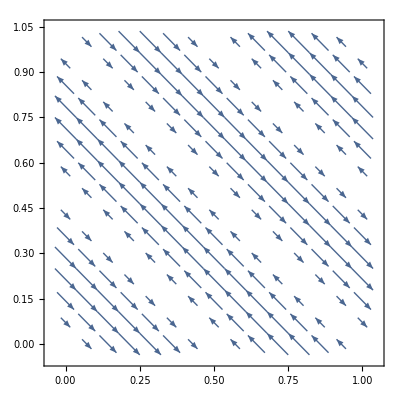

```mathematica
VectorPlot[w[x,y],{x,0,1},{y,0,1}, PlotLegends->Automatic]
```

```mathematica
u[x_,y_]=Part[w[x,y],1]
```

2 π Sin[2 π (x+y)]

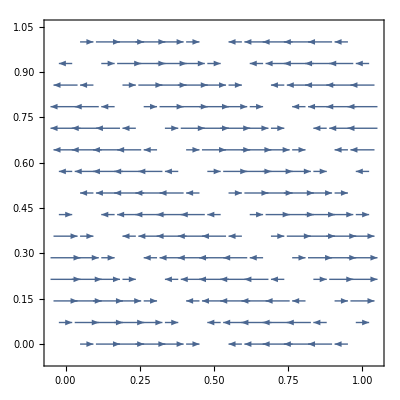

```mathematica
VectorPlot[{u[x,y],0},{x,0,1},{y,0,1}]
```

```mathematica
du[x_,y_]=Grad[u[x,y],{x,y}]
```

{4 π^2 Cos[2 π (x+y)],4 π^2 Cos[2 π (x+y)]}

```mathematica
w[x,y].du[x,y]
```

-2 π Sin[2 π (x+y)] u^(0,1)[x,y]+2 π Sin[2 π (x+y)] u^(1,0)[x,y]

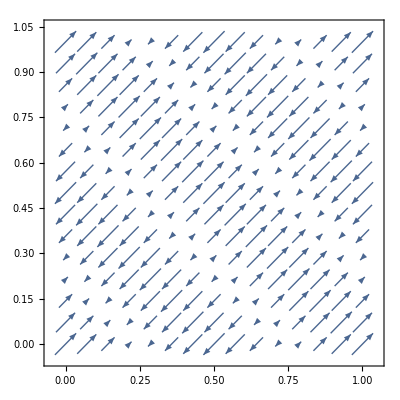

```mathematica
VectorPlot[du[x,y],{x,0,1},{y,0,1}]
```